# Maximizing Peak Area (and Peak Height)

## Eric Moyer

June 2013

## Introduction

In order to make the sampled distributions more accurate and avoid missing generated peak parameter values, I will augment the sampled distributions by setting the their maxima and minima to the true maxima and minima.

Peak height is generated by first selecting heights from a known distribution and then dividing them by the highest point in the resulting noiseless spectrum.

Peak areas are generated by a simple nonlinear formula (that is essentially a scaled product of the parameters). In hindsight (I am writing this introduction after doing the work) it should have been obvious that the maximum area came when you took the maximum of the two main parameters and let P be 1 (since  π>√(π/(log(2))))

The derivatives of the area are {1/2 G (P π+(1-P) √(π/Log[2])),1/2 M (P π+(1-P) √(π/Log[2])),1/2 G M (π-√(π/Log[2]))}. Note that since 0≤P≤1 and all other parameters are strictly positive, the derivative is always positive. So, the area is monotonic in each of the parameters.

The final result is:

scaled height range:  [ 0.00001604482555427710777509984241, 1 ]

area range: [2.93792276627387990798835084182×10^-8,0.070615230997076771515204158632]

## Work

### Calculate max area and max height

Formula for the area of a peak with the given height (M) width at half height (G) and Lorentzianness (P).

```mathematica
area[M_,G_,P_]:=(1/2) M G (P Pi+(1-P) Sqrt[Pi/Log[2]])
```

Take the first derivative with respect to each variable (glad I took Calc 3 :)

```mathematica
D[area[M,G,P],{{M,G,P}}]
```

{1/2 G (P π+(1-P) √(π/Log[2])),1/2 M (P π+(1-P) √(π/Log[2])),1/2 G M (π-√(π/Log[2]))}

Find the zeros of the derivative.

```mathematica
Solve[{1/2 G (P π+(1-P) √(π/Log[2]))==0,1/2 M (P π+(1-P) √(π/Log[2]))==0,1/2 G M (π-√(π/Log[2]))==0},{M,G,P}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{G→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{M→0,G→0},{M→0,G→0},{M→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{M→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))}}

The only unconstrained optima are where the area is 0. Double check using Mathematica's maximize routine.

```mathematica
Maximize[area[M,G,P],{M,G,P}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{M→-∞,G→-1,P→0}}

Now, look at the maxima where the height, width, and lorentzianness are constrained by the values from the original distributions.

Range of Lorentzianness: 0..1

Range of width-at-half-height:  [0.00172017711207981768, 0.0449550522830431884]

Range of height is more complicated because the heights in any spectrum are divided by the height of the highest point in that spectrum. The maximum height is 1 (put all the other peaks as far away as possible and make them as small as possible and their contribution to the largest peak will be negligable.) The minimum is the smallest original height divided by its height plus 6 times the largest original height (put all the peaks at one place and make 6 of them be maximum size.

Unscaled height range: [ 0.000191973000000000013, 1.99409999999999998 ]

min / (6*max + min):

```mathematica
maxOrigHeight =199409999999999998/100000000000000000
```

99704999999999999/50000000000000000

```mathematica
minOrigHeight=191973000000000013/1000000000000000000000
```

191973000000000013/1000000000000000000000

```mathematica
scaledMinHeight=minOrigHeight/(6*maxOrigHeight+minOrigHeight)
```

191973000000000013/11964791972999999880013

```mathematica
N[scaledMinHeight,28]
```

0.00001604482555427710777509984241

So, the range for scaled heights is: [ 0.00001604482555427710777509984241, 1 ]

```mathematica
Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,0.00172017711207981768≤G≤0.0449550522830431884},{M,G,P}]
```

{0.070615230997076772,{M→1.,G→0.04495505228304319,P→1.}}

Maximum area is attained by letting all the M,G, and P have their maximum values.

The minimum is probably the same - everything has its minimum value.

```mathematica
Minimize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,0.00172017711207981768≤G≤0.0449550522830431884},{M,G,P}]
```

{2.9379227662738799×10^-8,{M→0.00001604482555427711,G→0.001720177112079818,P→0}}

Hmmm. Not quite. Is that round-off error or a real problem. The equation looks like it will be round-off error, but better safe than sorry.

First, calculate the decimals as exact fractions.

```mathematica
minHalfHeightWidth=172017711207981768/100000000000000000000
```

21502213900997721/12500000000000000000

```mathematica
N[minHalfHeightWidth,25]
```

0.00172017711207981768

```mathematica
maxHalfHeightWidth=449550522830431884/10000000000000000000
```

112387630707607971/2500000000000000000

```mathematica
N[maxHalfHeightWidth,25]
```

0.0449550522830431884

Now do the minimize with exact numbers

```mathematica
Minimize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]
```

{(133156274490846315260057442353883 √(π/Log[2]))/9649025784677419258075000000000000000000,{M→191973000000000013/11964791972999999880013,G→21502213900997721/12500000000000000000,P→0}}

Check that the minimum found for the height is the minimum height

```mathematica
191973000000000013/11964791972999999880013-scaledMinHeight
```

0

Check that the minimum found for the width is the minimum bound for the width

```mathematica
21502213900997721/12500000000000000000-minHalfHeightWidth
```

0

So, everything went to its minimum value to give minimum area.

Finally, redo the maximize with exact numbers to get rid of any residual round-off error. It's not too important, but it's easy to do.

```mathematica
Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]
```

{(112387630707607971 π)/5000000000000000000,{M→1,G→112387630707607971/2500000000000000000,P→1}}

### Double-check assumption that height contribution of 6 distant small peaks is negligable

Width of most congested spectrum: 0.0260837320427020625

Function for Gauss-Lorentz Peak:

```mathematica
lorentzian[G_,x_,x0_]:=(G^2)/(4(x-x0)^2+G^2)
```

```mathematica
gaussian[G_,x_,x0_]:=Exp[-(x-x0)^2/(2 (G/2 Sqrt[2 Log[2]])^2)]
```

```mathematica
glp[M_,G_,P_,x_,x0_]:=M(P lorentzian[G,x,x0]+(1-P) gaussian[G,x,x0])
```

#### Make sure it looks right

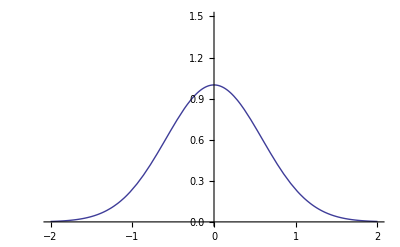

```mathematica
Plot[glp[1,1,0,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

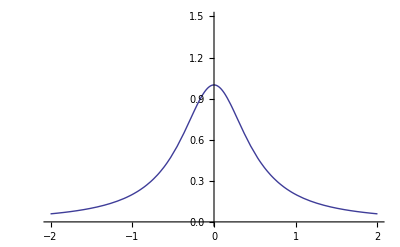

```mathematica
Plot[glp[1,1,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

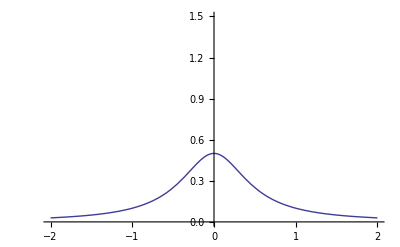

```mathematica
Plot[glp[0.5,1,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

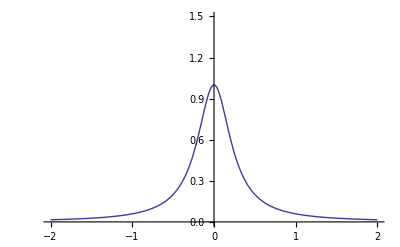

```mathematica
Plot[glp[1,0.5,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

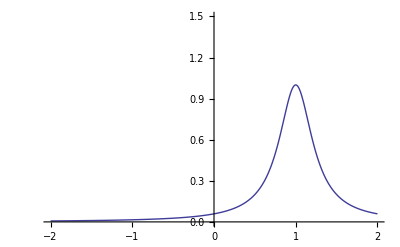

```mathematica
Plot[glp[1,0.5,1,x,1],{x,-2,2},PlotRange->{0,1.5}]
```

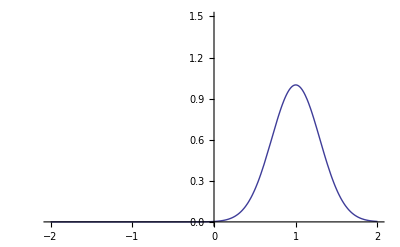

```mathematica
Plot[glp[1,0.5,0,x,1],{x,-2,2},PlotRange->{0,1.5}]
```

#### Use to calculate extreme spectrum

The spectrum with 7 peaks with the largest possible peak height will have 6 Gaussian peaks at one end of the spectrum (Gaussian so their tails are as small as possible), those peaks as small as can be and 1 peak of maximum height at the other end. I use the most congested spectrum to see how good the assumption is in the worst case.

```mathematica
mostCongestedSpecWidth=260837320427020625/10000000000000000000
```

417339712683233/16000000000000000

```mathematica
N[mostCongestedSpecWidth,20]
```

0.0260837320427020625

```mathematica
extremeSpectrum[x_]:=6 glp[minOrigHeight,minHalfHeightWidth,0,x,0]+glp[maxOrigHeight,minHalfHeightWidth,0,x,mostCongestedSpecWidth]
```

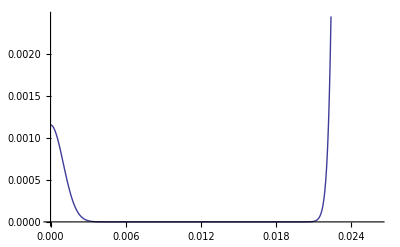

```mathematica
Plot[extremeSpectrum[x],{x,0,mostCongestedSpecWidth}]
```

Now, calculate the maximum scaled peak height

```mathematica
Maximize[{extremeSpectrum[x],0≤x≤mostCongestedSpecWidth},x]
```

Maximize::ztest1: Unable to decide whether numeric quantity -417339712683233 + 16000000000000000 Root[{-41610856053081745847660287316767 + 1595279999999999984000000000000000 Slot[« 1 »] + 921470400000000062400000000000 Power[« 2 »] Slot[« 1 »] &, « 185 »}] is equal to zero. Assuming it is.

{(ⅇ^(-1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])) (575919000000000039+997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2]))))/500000000000000000000,{x→417339712683233/16000000000000000}}

How different is the maximum scaled peak height from 1?

```mathematica
FullSimplify[1-(maxOrigHeight/extremeSpectrum[417339712683233/16000000000000000])]
```

1/(1+(997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])))/575919000000000039)

It is approximately 1+5*10^-148

```mathematica
N[1/(1+(997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])))/575919000000000039)]
```

4.99806×10^-148

Take the log base 2 to find out how many bits of precision would be needed:

```mathematica
N[Log[2,1/(1+(997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])))/575919000000000039)]]
```

-489.324

We'd need at least a 490 bit number to represent the number as different than 1. Since double precision only gives us 53 bits, we're quite safe. And since this is the MOST different than 1 it could be (since this is the most congested spectrum) we are safe in calling it 1 in all congestions.